```mathematica
SetDirectory[NotebookDirectory[] <> "MSE_LSV"]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/MSE_LSV

```mathematica
f=FileNames["*MSE*"]
```

{Rh_MM_MSE_BBT_future_BITW100.csv,Rh_MM_MSE_BBT_future_BITW20.csv,Rh_MM_MSE_BBT_future_BITW70.csv,Rh_MM_MSE_BBT_future_BITX.csv,Rh_MM_MSE_BBT_future_CRIX.csv,Rh_MM_MSE_BBT_future_Tiingo_ada.csv,Rh_MM_MSE_BBT_future_Tiingo_eth.csv,Rh_MM_MSE_BBT_future_Tiingo_ltc.csv,Rh_MM_MSE_BBT_future_Tiingo_xrp.csv,Rh_MM_MSE_BBT_Tiingo.csv}

```mathematica
titles=ToUpperCase[StringSplit[#,{"_","."}][[-2]]]&/@f
```

{BITW100,BITW20,BITW70,BITX,CRIX,ADA,ETH,LTC,XRP,TIINGO}

```mathematica
data = Import[#]&/@f
```

({,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.000137142,0.000142098,0.000173632,0.000138931,0.000148388,0.000138471} | {Frank,0.000321968,0.000487336,0.000274245,0.000500821,0.000378282,0.000433793} | {Gauss Mix Indep,0.000138668,0.000138168,0.000143315,0.000138189,0.00013896,0.000138215} | {Gaussian,0.000137452,0.000137585,0.000137938,0.000139633,0.000137433,0.000137958} | {Gumbel,0.000136966,0.000141742,0.000151812,0.000143146,0.000142151,0.000139609} | {NIG,0.00013624,0.00013729,0.000146017,0.000137417,0.000149709,0.000134585} | {Plackett,0.000138163,0.000138122,0.000140429,0.000138665,0.000138823,0.00013795} | {rotGumbel,0.000137899,0.000142021,0.000148824,0.000138321,0.00014394,0.000139985} | {t_Copula,0.000137652,0.00013762,0.000137474,0.000139011,0.000135314,0.00013811}
{,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.00130251,0.00132871,0.00135319,0.00133637,0.00136053,0.00132195} | {Frank,0.00127244,0.00128713,0.00137163,0.0013046,0.00128211,0.00129112} | {Gauss Mix Indep,0.00128823,0.0013023,0.00138351,0.00129751,0.0012945,0.00130072} | {Gaussian,0.00128114,0.00130153,0.00136787,0.00129324,0.00128957,0.00129759} | {Gumbel,0.00128277,0.00135844,0.00162034,0.00130844,0.00140589,0.00131861} | {NIG,0.00129188,0.00132127,0.00141027,0.00131812,0.00133225,0.00128577} | {Plackett,0.00127984,0.0012969,0.00135779,0.00128588,0.0012933,0.00129548} | {rotGumbel,0.00128748,0.0013059,0.00131255,0.00130164,0.00130672,0.00130207} | {t_Copula,0.00127684,0.00129506,0.00132845,0.00129174,0.00128847,0.00129437}
{,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.0015204,0.00157177,0.0015798,0.00156798,0.00160925,0.0015572} | {Frank,0.00149689,0.00149961,0.00155352,0.00150666,0.00150367,0.00150075} | {Gauss Mix Indep,0.00154541,0.00156605,0.00166453,0.0015159,0.00161078,0.00153151} | {Gaussian,0.00150205,0.00150602,0.0015619,0.00150849,0.00150936,0.00150818} | {Gumbel,0.00151625,0.00156547,0.00180441,0.00151892,0.00161691,0.00152489} | {NIG,0.00154793,0.00155867,0.00163756,0.00152098,0.00161508,0.001623} | {Plackett,0.00151144,0.00151723,0.00154251,0.00150899,0.00152239,0.0015136} | {rotGumbel,0.0015055,0.00152361,0.00153316,0.00153135,0.00152211,0.00152409} | {t_Copula,0.00152606,0.00151682,0.00157878,0.00151534,0.00152823,0.0015217}
{,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.0000988751,0.000101211,0.000132775,0.0000983154,0.00011,0.0000985119} | {Frank,0.000278954,0.00044196,0.000237181,0.00049278,0.000340637,0.000386673} | {Gauss Mix Indep,0.0000992942,0.0000977495,0.000103737,0.0000981443,0.0000985992,0.00009817} | {Gaussian,0.0000980181,0.000097622,0.000097829,0.0000989146,0.0000971593,0.0000980059} | {Gumbel,0.000097775,0.000101976,0.000112308,0.000102229,0.000102975,0.0001002} | {NIG,0.0000976997,0.000097843,0.000102052,0.0000990137,0.000103793,0.0000982082} | {Plackett,0.0000987601,0.0000976177,0.0000995295,0.0000983743,0.0000991544,0.0000983162} | {rotGumbel,0.0000982228,0.000100477,0.000107951,0.0000964075,0.000102872,0.0000995026} | {t_Copula,0.0000987151,0.0000980725,0.0000995503,0.0000979673,0.0000979395,0.0000982466}
{,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.0000887185,0.0000885156,0.000114436,0.0000860698,0.0000925031,0.0000857029} | {Frank,0.000241315,0.000418104,0.000228484,0.000184818,0.000351949,0.000316149} | {Gauss Mix Indep,0.0000855737,0.0000841366,0.0000925625,0.0000870951,0.0000882327,0.000084911} | {Gaussian,0.0000847619,0.0000844777,0.0000847516,0.0000871451,0.0000847923,0.0000848623} | {Gumbel,0.0000847087,0.0000871371,0.0000963062,0.0000876007,0.0000881828,0.0000856218} | {NIG,0.0000848466,0.0000846783,0.0000946237,0.0000838576,0.0000947708,0.0000831122} | {Plackett,0.0000861151,0.0000851148,0.0000871559,0.000086114,0.0000874549,0.0000853281} | {rotGumbel,0.0000848305,0.0000882413,0.0000924562,0.000085733,0.0000888688,0.0000870544} | {t_Copula,0.0000847856,0.0000841701,0.0000844839,0.0000853593,0.0000852238,0.0000847503}
{,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.00301195,0.00303744,0.0030609,0.00301403,0.00306711,0.00302631} | {Frank,0.00305919,0.00303569,0.00309537,0.00302215,0.0030228,0.00302513} | {Gauss Mix Indep,0.00304946,0.0030571,0.00319511,0.00299593,0.00309781,0.00299922} | {Gaussian,0.00305002,0.00303672,0.00312465,0.00300271,0.00305051,0.003005} | {Gumbel,0.00303041,0.00306922,0.00335807,0.00300283,0.00312324,0.00301192} | {NIG,0.00305016,0.00304273,0.00317151,0.00300167,0.00312098,0.00314125} | {Plackett,0.00303753,0.00300177,0.00300864,0.00301161,0.00298455,0.00300078} | {rotGumbel,0.00303209,0.00300084,0.00300855,0.00299583,0.00300222,0.00299918} | {t_Copula,0.00303584,0.00299597,0.00307387,0.0029943,0.00299753,0.00298779}
{,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.00164269,0.0016867,0.00172665,0.00163648,0.00172824,0.00166377} | {Frank,0.00164575,0.00163994,0.00165334,0.00165399,0.00165821,0.00163968} | {Gauss Mix Indep,0.00166082,0.00164748,0.00176362,0.00162052,0.00165443,0.00164123} | {Gaussian,0.00164496,0.0016309,0.00168014,0.00165022,0.00162812,0.00163122} | {Gumbel,0.0016417,0.00172832,0.00200646,0.00165305,0.00182984,0.00166349} | {NIG,0.0016616,0.00167575,0.00179916,0.00162434,0.00172727,0.00166468} | {Plackett,0.00164606,0.00163506,0.0016328,0.00164789,0.00163245,0.00163663} | {rotGumbel,0.00164452,0.00164735,0.00165241,0.00165842,0.00164699,0.00164832} | {t_Copula,0.0016589,0.00164515,0.00167995,0.00166335,0.00163891,0.00164605}
{,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.00148729,0.00159032,0.0016715,0.0015023,0.00161796,0.00155948} | {Frank,0.00147531,0.00146343,0.00148922,0.00149105,0.00148163,0.00146336} | {Gauss Mix Indep,0.00149506,0.0015279,0.0017008,0.00146247,0.00163189,0.00148252} | {Gaussian,0.0014668,0.00144937,0.00148074,0.00148303,0.00145504,0.00145937} | {Gumbel,0.00147898,0.00152311,0.00177743,0.00146246,0.00159427,0.00146944} | {NIG,0.00149377,0.00155027,0.00169069,0.00149666,0.0016591,0.0014873} | {Plackett,0.00148939,0.0014827,0.00149618,0.00149906,0.0015296,0.00147814} | {rotGumbel,0.00146925,0.00151944,0.00155198,0.00150123,0.00154138,0.00151114} | {t_Copula,0.00147965,0.00147609,0.00155894,0.00148468,0.00148928,0.00147422}
{,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.00589889,0.00591396,0.00608756,0.00593686,0.00591688,0.00591871} | {Frank,0.00592522,0.00590067,0.00613468,0.00590078,0.00593582,0.00589612} | {Gauss Mix Indep,0.00595707,0.00595249,0.0063033,0.00590261,0.00599905,0.00590751} | {Gaussian,0.00595264,0.00592722,0.00622512,0.00589705,0.00594058,0.00589802} | {Gumbel,0.00593811,0.00596904,0.00639804,0.00592454,0.00603415,0.00592866} | {NIG,0.00599268,0.00596112,0.00631269,0.00589212,0.00601235,0.00594407} | {Plackett,0.00591475,0.00589336,0.00607343,0.00589789,0.00590057,0.00589928} | {rotGumbel,0.00593915,0.00590674,0.00612742,0.00590809,0.00591328,0.00590305} | {t_Copula,0.00611575,0.00604679,0.00630063,0.00597756,0.00601263,0.00601285}
{,Variance,ES q=0.05,ES q=0.01,VaR q=0.05,VaR q=0.01,ERM k=10} | {Clayton,0.000126625,0.0000130961,0.0000255417,0.000011346,0.0000151944,0.0000119831} | {Frank,0.000195372,0.000378681,0.000158956,0.000191934,0.000278451,0.000308853} | {Gauss Mix Indep,0.0000111088,0.0000110697,0.0000118128,0.0000110329,0.0000111874,0.000011011} | {Gaussian,0.0000109616,0.0000108758,0.0000117137,0.0000109886,0.0000108818,0.0000108242} | {Gumbel,0.0000109176,0.0000131167,0.0000188828,0.0000111789,0.0000145037,0.0000120093} | {NIG,0.000010139,0.0000105078,0.0000128408,0.0000109583,0.0000115671,0.0000101943} | {Plackett,0.0000107995,0.0000108172,0.0000114669,0.0000107049,0.0000110387,0.0000107704} | {rotGumbel,0.0000109762,0.0000107579,0.0000110321,0.0000111688,0.0000105408,0.0000107998} | {t_Copula,0.000010886,0.0000109135,0.000011354,0.0000112304,0.0000110409,0.0000108404})

```mathematica
data[[;;,2;;,2;;]]=100 data[[;;,2;;,2;;]];
```

```mathematica
{min,max}=MinMax[data[[;;,2;;,2;;]]]
```

{0.0010139,0.639804}

```mathematica
methods={"Variance","VaR 99%","VaR 95%","ES 99%","ES 95%","Spectral 10"};
measures =methods;
copulas={"Clayton","Frank","Gaussian","Gauss Mix Indep","Gumbel","Plackett","t_Copula","t_Copula_Capped","NIG Factor"};
```

```mathematica
o={3,7,1,2,5,6,9,4}; (* ordering *)
```

```mathematica
ticks1 = Table[{ii,measures[[ii]]}, {ii, 1, Length[measures]}];
ticks2 = Table[{ii,copulas[[o[[ii]]]]}, {ii, 1, Length[o]}];
```

```mathematica
data[[2;;,1]]
```

( | Variance | ES q=0.05 | ES q=0.01 | VaR q=0.05 | VaR q=0.01 | ERM k=10
 | Variance | ES q=0.05 | ES q=0.01 | VaR q=0.05 | VaR q=0.01 | ERM k=10
 | Variance | ES q=0.05 | ES q=0.01 | VaR q=0.05 | VaR q=0.01 | ERM k=10
 | Variance | ES q=0.05 | ES q=0.01 | VaR q=0.05 | VaR q=0.01 | ERM k=10
 | Variance | ES q=0.05 | ES q=0.01 | VaR q=0.05 | VaR q=0.01 | ERM k=10
 | Variance | ES q=0.05 | ES q=0.01 | VaR q=0.05 | VaR q=0.01 | ERM k=10
 | Variance | ES q=0.05 | ES q=0.01 | VaR q=0.05 | VaR q=0.01 | ERM k=10
 | Variance | ES q=0.05 | ES q=0.01 | VaR q=0.05 | VaR q=0.01 | ERM k=10
 | Variance | ES q=0.05 | ES q=0.01 | VaR q=0.05 | VaR q=0.01 | ERM k=10)

```mathematica
data[[1,2;;]]
```

(Clayton | 0.0137142 | 0.0142098 | 0.0173632 | 0.0138931 | 0.0148388 | 0.0138471
Frank | 0.0321968 | 0.0487336 | 0.0274245 | 0.0500821 | 0.0378282 | 0.0433793
Gauss Mix Indep | 0.0138668 | 0.0138168 | 0.0143315 | 0.0138189 | 0.013896 | 0.0138215
Gaussian | 0.0137452 | 0.0137585 | 0.0137938 | 0.0139633 | 0.0137433 | 0.0137958
Gumbel | 0.0136966 | 0.0141742 | 0.0151812 | 0.0143146 | 0.0142151 | 0.0139609
NIG | 0.013624 | 0.013729 | 0.0146017 | 0.0137417 | 0.0149709 | 0.0134585
Plackett | 0.0138163 | 0.0138122 | 0.0140429 | 0.0138665 | 0.0138823 | 0.013795
rotGumbel | 0.0137899 | 0.0142021 | 0.0148824 | 0.0138321 | 0.014394 | 0.0139985
t_Copula | 0.0137652 | 0.013762 | 0.0137474 | 0.0139011 | 0.0135314 | 0.013811)

```mathematica
Dimensions[rrmse]
```

{9,6}

```mathematica
ticks1
```

(1 | Variance
2 | VaR 99%
3 | VaR 95%
4 | ES 99%
5 | ES 95%
6 | Spectral 10)

```mathematica
titles
```

{BITW100,BITW20,BITW70,BITX,CRIX,ADA,ETH,LTC,XRP,TIINGO}

```mathematica
data[[o1[[1]], 2;;,2;;]]
```

(0.00887185 | 0.00885156 | 0.0114436 | 0.00860698 | 0.00925031 | 0.00857029
0.0241315 | 0.0418104 | 0.0228484 | 0.0184818 | 0.0351949 | 0.0316149
0.00855737 | 0.00841366 | 0.00925625 | 0.00870951 | 0.00882327 | 0.0084911
0.00847619 | 0.00844777 | 0.00847516 | 0.00871451 | 0.00847923 | 0.00848623
0.00847087 | 0.00871371 | 0.00963062 | 0.00876007 | 0.00881828 | 0.00856218
0.00848466 | 0.00846783 | 0.00946237 | 0.00838576 | 0.00947708 | 0.00831122
0.00861151 | 0.00851148 | 0.00871559 | 0.0086114 | 0.00874549 | 0.00853281
0.00848305 | 0.00882413 | 0.00924562 | 0.0085733 | 0.00888688 | 0.00870544
0.00847856 | 0.00841701 | 0.00844839 | 0.00853593 | 0.00852238 | 0.00847503)

```mathematica
o1={5,4,1,2,3,6,7,8,9};
```

```mathematica
MinMax[d]
```

{0.00831122,0.0418104}

```mathematica
max
```

0.639804

```mathematica
Rescale[d,MinMax[d]]/max
```

(0.0261573 | 0.738129 | 0.0114846 | 0.00769691 | 0.00744853 | 0.00809205 | 0.0140106 | 0.00801695 | 0.00780737
0.0252104 | 1.56298 | 0.00477931 | 0.00637109 | 0.0187792 | 0.00730687 | 0.00934347 | 0.0239307 | 0.00493571
0.146148 | 0.678265 | 0.0440926 | 0.007649 | 0.0615595 | 0.0537095 | 0.0188666 | 0.0435965 | 0.00639964
0.0137994 | 0.474531 | 0.0185829 | 0.0188163 | 0.0209421 | 0.00347778 | 0.0140054 | 0.0122278 | 0.0104843
0.0438154 | 1.25432 | 0.0238909 | 0.00783872 | 0.023658 | 0.0543956 | 0.0202615 | 0.0268585 | 0.00985222
0.0120875 | 1.08728 | 0.00839247 | 0.0081656 | 0.0117089 | 0. | 0.0103386 | 0.0183932 | 0.00764301)

```mathematica
(ColorData["BlueGreenYellow"][Rescale[#,MinMax[Log[d]]]]&)
```

ColorData[BlueGreenYellow][Rescale[#1,MinMax[log(d)]]]&

```mathematica
k=1;
```

```mathematica
d=data[[o1[[k]],2;;,2;;]]ᵀ
```

(0.00887185 | 0.0241315 | 0.00855737 | 0.00847619 | 0.00847087 | 0.00848466 | 0.00861151 | 0.00848305 | 0.00847856
0.00885156 | 0.0418104 | 0.00841366 | 0.00844777 | 0.00871371 | 0.00846783 | 0.00851148 | 0.00882413 | 0.00841701
0.0114436 | 0.0228484 | 0.00925625 | 0.00847516 | 0.00963062 | 0.00946237 | 0.00871559 | 0.00924562 | 0.00844839
0.00860698 | 0.0184818 | 0.00870951 | 0.00871451 | 0.00876007 | 0.00838576 | 0.0086114 | 0.0085733 | 0.00853593
0.00925031 | 0.0351949 | 0.00882327 | 0.00847923 | 0.00881828 | 0.00947708 | 0.00874549 | 0.00888688 | 0.00852238
0.00857029 | 0.0316149 | 0.0084911 | 0.00848623 | 0.00856218 | 0.00831122 | 0.00853281 | 0.00870544 | 0.00847503)

```mathematica
Rescale[d, MinMax[d]]
```

(0.0167355 | 0.472258 | 0.00734788 | 0.00492452 | 0.0047656 | 0.00517732 | 0.00896405 | 0.00512928 | 0.00499519
0.0161297 | 1. | 0.00305782 | 0.00407625 | 0.012015 | 0.00467497 | 0.00597799 | 0.0153109 | 0.00315789
0.0935058 | 0.433957 | 0.0282106 | 0.00489386 | 0.039386 | 0.0343635 | 0.012071 | 0.0278932 | 0.00409451
0.00882889 | 0.303607 | 0.0118894 | 0.0120388 | 0.0133988 | 0.0022251 | 0.00896071 | 0.00782342 | 0.00670792
0.0280332 | 0.802518 | 0.0152855 | 0.00501524 | 0.0151365 | 0.0348025 | 0.0129634 | 0.0171842 | 0.00630349
0.00773362 | 0.695648 | 0.00536954 | 0.00522439 | 0.00749141 | 0. | 0.00661469 | 0.0117681 | 0.00489003)

```mathematica
Max[d] max
```

0.0267505

```mathematica
Min[d]
```

0.00831122

```mathematica
Rescale[d, {0, Max[d]}]
```

(0.212192 | 0.577164 | 0.204671 | 0.202729 | 0.202602 | 0.202932 | 0.205966 | 0.202893 | 0.202786
0.211707 | 1. | 0.201234 | 0.20205 | 0.20841 | 0.202529 | 0.203573 | 0.211051 | 0.201314
0.273702 | 0.546477 | 0.221386 | 0.202705 | 0.23034 | 0.226316 | 0.208455 | 0.221132 | 0.202064
0.205857 | 0.442038 | 0.20831 | 0.208429 | 0.209519 | 0.200566 | 0.205963 | 0.205052 | 0.204158
0.221244 | 0.841774 | 0.211031 | 0.202802 | 0.210911 | 0.226668 | 0.20917 | 0.212552 | 0.203834
0.20498 | 0.756149 | 0.203086 | 0.202969 | 0.204786 | 0.198784 | 0.204083 | 0.208212 | 0.202702)

```mathematica
ColorData["BlueGreenYellow"]
```

ColorDataFunction[…]

```mathematica
(ColorData["BlueGreenYellow"][Rescale[d,{0,Max[d]}]])
```

Blend[BlueGreenYellow,(0.212192 | 0.577164 | 0.204671 | 0.202729 | 0.202602 | 0.202932 | 0.205966 | 0.202893 | 0.202786
0.211707 | 1. | 0.201234 | 0.20205 | 0.20841 | 0.202529 | 0.203573 | 0.211051 | 0.201314
0.273702 | 0.546477 | 0.221386 | 0.202705 | 0.23034 | 0.226316 | 0.208455 | 0.221132 | 0.202064
0.205857 | 0.442038 | 0.20831 | 0.208429 | 0.209519 | 0.200566 | 0.205963 | 0.205052 | 0.204158
0.221244 | 0.841774 | 0.211031 | 0.202802 | 0.210911 | 0.226668 | 0.20917 | 0.212552 | 0.203834
0.20498 | 0.756149 | 0.203086 | 0.202969 | 0.204786 | 0.198784 | 0.204083 | 0.208212 | 0.202702)]

```mathematica
MinMax[data[[;;,2;;,2;;]]]
```

{0.0010139,0.639804}

```mathematica
data2=Rescale[data[[o1,2;;,2;;]],{0,max}];
```

```mathematica
Log[0]
```

-∞

```mathematica
Log[min]
```

-6.89395

```mathematica
Log[max]
```

-0.446593

```mathematica
(ColorData["Rainbow"][Rescale[#,MinMax[rrmse[[o]]]]]&),MinMax[rrmse[[o]]]
```

```mathematica
(ColorData["Rainbow"][Rescale[#,MinMax[rrmse[[o]]]]]&)
```

```mathematica
p1=Table[d=data2[[o1[[k]]]]ᵀ;ArrayPlot[Log[d],(*FrameTicks->{{data[[2;;,1]],None},{data[[1,2;;]],None}},*)ColorFunction->"BlueGreenYellow",ColorFunctionScaling->True, FrameTicksStyle->Directive[Black, 12, FontFamily->"Times"],PlotLegends->Placed[BarLegend[{(ColorData["BlueGreenYellow"][Rescale[#,{min,max}]]&),{min,max}},LegendMarkerSize->200,LabelStyle->Directive[Black,12,FontFamily->"Times"]],{1.,0.5}],FrameLabel->{{None,titles[[o1[[k]]]]},{None,None}}], {k,1,Length[o1]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
p1=Table[d=data[[o1[[k]],2;;,2;;]]ᵀ/max;ArrayPlot[d,(*FrameTicks->{{data[[2;;,1]],None},{data[[1,2;;]],None}},*)ColorFunction->"BlueGreenYellow",ColorFunctionScaling->False, FrameTicksStyle->Directive[Black, 12, FontFamily->"Times"],PlotLegends->Placed[BarLegend[{ColorData["BlueGreenYellow"],{0,1}},LegendMarkerSize->200,LabelStyle->Directive[Black,12,FontFamily->"Times"]],{1.,0.5}],FrameLabel->{{None,titles[[o1[[k]]]]},{None,None}}], {k,1,Length[o1]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
p1=ArrayPlot[100rrmseᵀ,(*FrameTicks->{{data[[2;;,1]],None},{data[[1,2;;]],None}},*)ColorFunction->"Rainbow",ColorFunctionScaling->True, FrameTicksStyle->Directive[Black, 12, FontFamily->"Times"],PlotLegends->Automatic(*,PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][Rescale[#,MinMax[rrmse[[o]]]]]&),MinMax[rrmse[[o]]]},LegendMarkerSize->500,LabelStyle->Directive[Black,12,FontFamily->"Times"]],{1.,0.5}]*)]
```

-Graphics-

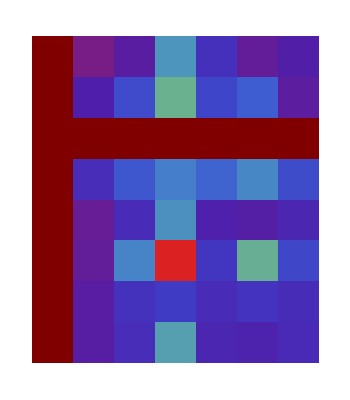

```mathematica
p1=ArrayPlot[Log[rrmse[[o]]],FrameTicks->{{ticks2,None},{ticks1,None}},ColorFunction->"Rainbow",ColorFunctionScaling->True, FrameTicksStyle->Directive[Black, 12, FontFamily->"Times"],
PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][Rescale[#,MinMax[rrmse[[o]]]]]&),MinMax[rrmse[[o]]]},LegendMarkerSize->500,LabelStyle->Directive[Black,15,FontFamily->"Times"]],{1.,0.5}]]
```